```mathematica
Integrate[Exp[-0.1/x],{x,1,2.6}]
```

1.50746

```mathematica
f[x_]:=Piecewise[{{x/7 + 1,x<0},{1,x>=0}}]
```

5/7

1

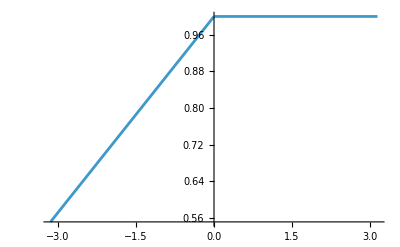

```mathematica
f[-2]
f[1]
Plot[f[x],{x,-Pi,Pi}]
```

```mathematica
a0=(1/Pi) NIntegrate[f[x],{x,-Pi,Pi}]
```

1.7756

```mathematica
a[n_]:=(1/Pi) NIntegrate[f[x] Cos[n x],{x,-Pi,Pi},Method->{"GaussKronrodRule","Points"->15}]
```

```mathematica
b[n_]:=(1/Pi) NIntegrate[f[x] Sin[n x],{x,-Pi,Pi}]
```

```mathematica
a[1]
```

0.0909457

```mathematica
b[1]
```

0.909859

```mathematica
a[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.081242}. NIntegrate obtained -7.35523×10^-16 and 5.04238×10^-16 for the integral and error estimates.

-2.34124×10^-16

```mathematica
b[2]
```

0.5

```mathematica
a[3]
```

0.0101051

```mathematica
b[3]
```

0.303286

```mathematica
a[4]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.1415925972447566019283762852398820663440970335500423971097916365}. NIntegrate obtained 4.71845×10^-16 and 2.3287×10^-12 for the integral and error estimates.

1.50193×10^-16

```mathematica
b[4]
```

0.25

```mathematica
a[5]
```

-0.0254648

```mathematica
b[5]
```

0.181972